```mathematica
Clear["Global*`"]
```

```mathematica
U[n_, mu_, nu_]:=∑_(k=0)^20 (-1)^k (mu/nu)^(n+2 k) BesselJ[n+2k, Pi mu nu];
```

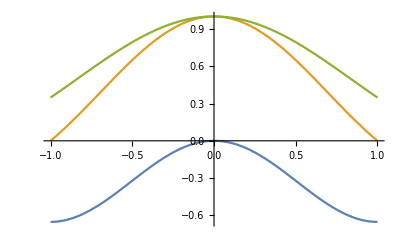

```mathematica
Plot[{U[0, 1, x], U[1, 1, x], U[2, 1, x]}, {x, -1, 1}]
```

```mathematica
Int[rho_, eta_]:=Piecewise[{{U[0, rho, eta]^2 + U[1, rho, eta]^2, Abs[eta]≤ rho}, {1+U[1, rho, eta]^2+U[2, rho, eta]^2-2 U[1, rho, eta] Sin[Pi/2 (rho^2+eta^2)]+2 U[2, rho, eta] Cos[Pi/2 (rho^2+eta^2)], Abs[eta]≥ rho}}]
```

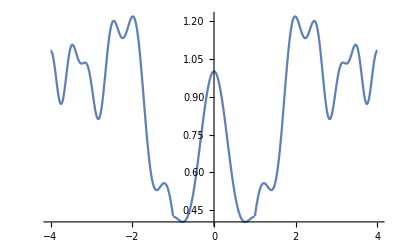

```mathematica
Plot[Int[1, eta], {eta, -4, 4}]
```